Pade approximation of magnetic susceptibility for P[1,11]

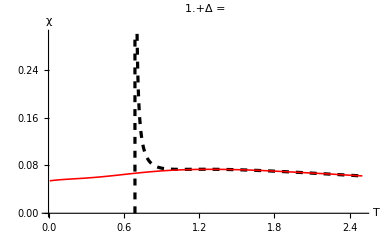

Pade approximation of magnetic susceptibility for P[2,10]

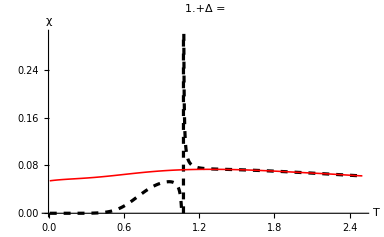

Pade approximation of magnetic susceptibility for P[3,9]

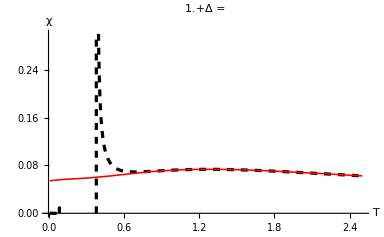

Pade approximation of magnetic susceptibility for P[4,8]

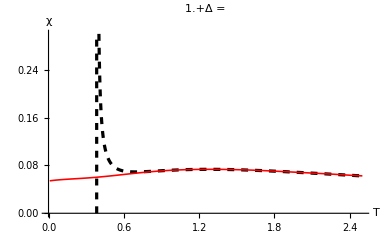

Pade approximation of magnetic susceptibility for P[5,7]

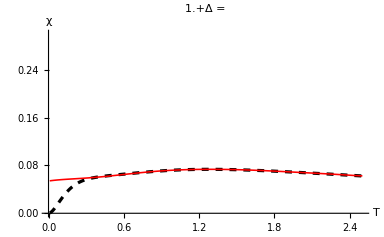

Pade approximation of magnetic susceptibility for P[6,6]

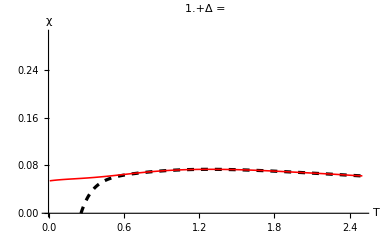

Pade approximation of magnetic susceptibility for P[7,5]

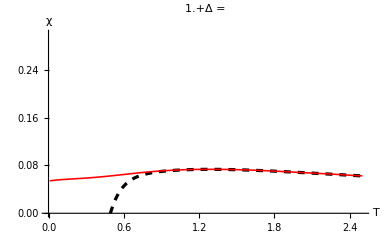

Pade approximation of magnetic susceptibility for P[8,4]

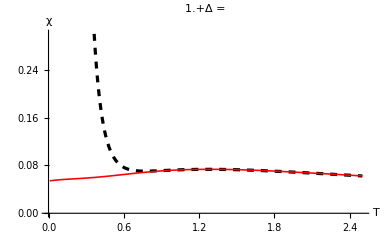

Pade approximation of magnetic susceptibility for P[9,3]

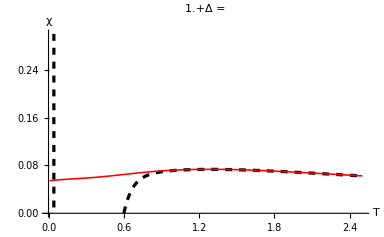

Pade approximation of magnetic susceptibility for P[10,2]

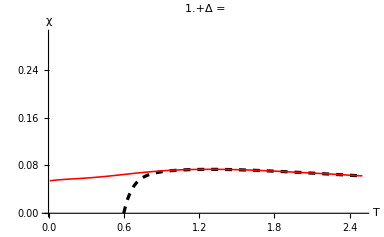

Pade approximation of magnetic susceptibility for P[11,1]

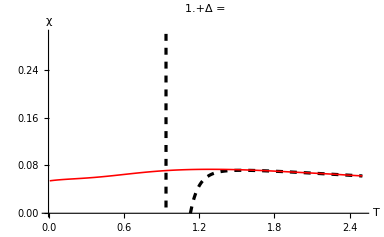

```mathematica
(*Data QTM*)
(*QTM data obtained from the work of Klumber for J = 2*)
(*Klümper,A.(2008).Integrability of quantum chains:theory and applications to the spin-1/2 XXZ chain.Quantum magnetism,349-379.*)
(*Arxiv: https://arxiv.org/pdf/cond-mat/0502431*)
(*Magnetic susceptibility *)
QTMsuc={{{0.01,0.15916148977334485},{0.02,0.15918115023209922},{0.03,0.1592139861155509},{0.04,0.1592601015448771},{0.05,0.15931964528961515},{0.060000000000000005,0.1593928140506827},{0.06999999999999999,0.15947985717310587},{0.08,0.15958108337239038},{0.09,0.15969687061776183},{0.09999999999999999,0.1598276811188905},{0.11,0.15997408322417114},{0.12,0.1601367792175519},{0.13,0.16031663276910973},{0.14,0.1605146854470133},{0.15000000000000002,0.16073215152443598},{0.16,0.16097038475205747},{0.17,0.16123081748009593},{0.18000000000000002,0.16151487862207548},{0.19,0.16182390059756457},{0.2,0.16215902618584527},{0.3,0.1669489980199531},{0.4,0.17312012747127678},{0.5,0.17815619949508568},{0.6000000000000001,0.18054366910833278},{0.7,0.1800842755307345},{0.8,0.17727591281541993},{0.9000000000000001,0.17280063958433198},{1.,0.1672774281526582},{1.1,0.1611855290567975},{1.2,0.15486530900585085},{1.3,0.14854471881096462},{1.4000000000000001,0.14236882666944414},{1.5000000000000002,0.1364246894142789},{1.6,0.1307601048954992},{1.7000000000000002,0.12539698370286367},{1.8,0.12034058571161252},{1.9000000000000001,0.11558577381814786},{2.,0.111121187905598},{2.1,0.10693199662090533},{2.2,0.10300168802203678},{2.3,0.09931321571069585},{2.4,0.0958497153524792},{2.5,0.09259493649507582},{2.6,0.08953348703454124},{3.,0.07894806149487718},{3.4000000000000004,0.07048122592497806},{3.8000000000000003,0.06358782339683018},{4.2,0.05788320141511768},{4.6,0.053093297036550594},{5.,0.04901962899017651},{5.4,0.045515858683638166},{5.800000000000001,0.04247218098137077},{6.2,0.03980483271335307},{6.6,0.03744893636568417},{7.,0.03535353740873672},{7.4,0.03347810490728411},{7.800000000000001,0.03179002379192276},{8.200000000000001,0.03026277009609726},{8.6,0.028874564014679627},{9.,0.02760736232061823},{9.4,0.026446095244833816},{9.8,0.025378081821597426}},{{2.493891021176634,0.08923636880418133},{2.4546201101835403,0.09035925265061996},{2.42516692693872,0.09120141553544892},{2.382623440029535,0.09260502034349719},{2.3433525290364408,0.09372790418993582},{2.2942638902950736,0.09541222995959373},{2.2582655552180713,0.09653511380603233},{2.2255397960571597,0.09765799765247096},{2.173178581399701,0.09934232342212887},{2.110999638993969,0.10158809111500611},{2.05536584842042,0.1035531378462737},{1.9931869060146878,0.10579890553915092},{1.957188570937685,0.10748323130880885},{1.9310079636089557,0.10832539419363782},{1.888464476699771,0.11000971996329574},{1.8393758379584035,0.11225548765617296},{1.803377502881401,0.11365909246422123},{1.741198560475669,0.11646630208031777},{1.6921099217343016,0.11871206977319501},{1.6561115866572986,0.12039639554285293},{1.6168406756642049,0.12208072131251085},{1.5677520369228377,0.12432648900538809},{1.531753701845835,0.12629153573665566},{1.4990279426849236,0.12797586150631357},{1.466302183524012,0.12937946631436187},{1.4303038484470092,0.13134451304562944},{1.3877603615378242,0.133309559776897},{1.3517620264608214,0.1352746065081646},{1.312491115467728,0.13723965323943216},{1.2732202044746341,0.13920469997069976},{1.2339492934815401,0.1411697467019673},{1.207768686152811,0.1425733515100156},{1.1815880788240816,0.14397695631806384},{1.1357720159988054,0.1462227240109411},{1.106318832753985,0.14762632881898935},{1.0637753458448,0.14959137555025695},{1.0343221625999797,0.15099498035830522},{1.001596403439068,0.1523985851663535},{0.9623254924459742,0.15408291093601142},{0.9328723092011539,0.15520579478245006},{0.9099642777885159,0.15604795766727897},{0.8968739741241514,0.1566093995904983},{0.8608756390471485,0.1577322834369369},{0.8379676076345104,0.15829372536015623},{0.8052418484735991,0.1591358882449852},{0.7659709374805053,0.15969733016820448},{0.7365177542356847,0.1602587720914238},{0.6972468432425908,0.16053949305303344},{0.6579759322494969,0.16053949305303344},{0.6285227490046766,0.15997805112981411},{0.5957969898437651,0.15941660920659484},{0.546708351102398,0.15829372536015623},{0.4976197123610306,0.1566093995904983},{0.464893953200119,0.15520579478245006},{0.43871334587138966,0.15408291093601142},{0.40926016262656933,0.1523985851663535},{0.36671667571738453,0.15015281747347625},{0.3339909165564729,0.14846849170381834},{0.31435546105992584,0.14762632881898935},{0.2849022778151055,0.1462227240109411},{0.24563136682201167,0.14453839824128317},{0.21617818357719137,0.1436962353564542},{0.18672500033237105,0.14285407247162524},{0.15072666525536818,0.14201190958679633},{0.1114557542622744,0.141450467663577},{0.07545741918527168,0.1411697467019673},{0.04273166002436025,0.14088902574035767},{0.010005900863448653,0.14088902574035767}},{{2.493891021176634,0.08558699630325586},{2.4677104138479047,0.0864291591880848},{2.431712078770902,0.08727132207291377},{2.3989863196099908,0.08811348495774274},{2.3433525290364408,0.08979781072740066},{2.300809042127256,0.09092069457383928},{2.2484478274697977,0.09260502034349721},{2.2189946442249773,0.09344718322832615},{2.182996309147974,0.09457006707476479},{2.1437253981548805,0.09597367188281306},{2.1044544871617865,0.09709655572925166},{2.0717287280008754,0.09821943957569028},{2.0455481206721458,0.09906160246051923},{2.019367513343417,0.0999037653453482},{1.9997320578468698,0.10074592823017717},{1.976824026434232,0.10158809111500613},{1.9440982672733202,0.10243025399983509},{1.9146450840284999,0.10355313784627371},{1.888464476699771,0.10439530073110266},{1.852466141622768,0.10579890553915094},{1.8328306861262211,0.10664106842397991},{1.8001049269653095,0.10776395227041852},{1.7706517437204894,0.10888683611685712},{1.7379259845595776,0.1102904409249054},{1.701927649482575,0.11169404573295368},{1.6724744662377544,0.11281692957939228},{1.6430212829929343,0.1139398134258309},{1.6102955238320227,0.11534341823387918},{1.5677520369228377,0.11674702304192744},{1.531753701845835,0.11843134881158536},{1.4990279426849236,0.11983495361963363},{1.466302183524012,0.12123855842768191},{1.4270312725309182,0.12292288419733984},{1.3975780892860978,0.12404576804377845},{1.3713974819573684,0.12516865189021706},{1.3386717227964569,0.12657225669826533},{1.292855659971181,0.12825658246792326},{1.2568573248941783,0.1299409082375812},{1.2241315657332668,0.13134451304562944},{1.1914058065723552,0.13246739689206805},{1.1652251992436258,0.13359028073850665},{1.1324994400827144,0.1347131645849453},{1.0997736809218028,0.13583604843138392},{1.0670479217608912,0.13695893227782255},{1.0375947385160709,0.13808181612426115},{1.0048689793551593,0.13920469997069976},{0.9655980683620655,0.14032758381713836},{0.9263271573689716,0.141450467663577},{0.8870562463758778,0.14229263054840596},{0.8608756390471485,0.1428540724716253},{0.8281498798862372,0.14313479343323493},{0.7954241207253255,0.14341551439484457},{0.7692435133965962,0.14369623535645426},{0.739790330151776,0.14369623535645426},{0.7103371469069556,0.14369623535645426},{0.6841565395782263,0.14341551439484457},{0.6350679008368589,0.1428540724716253},{0.5827066861794006,0.14173118862518663},{0.5303454715219422,0.14004686285552873},{0.48452940869666605,0.13808181612426115},{0.43216819403920737,0.13583604843138392},{0.3863521312139313,0.13387100170011634},{0.3405360683886552,0.13190595496884877},{0.28162970189901454,0.1296601872759715},{0.21945075949328266,0.12797586150631363},{0.17363469666800624,0.12685297765987497},{0.12127348201054794,0.1262915357366557},{0.08200257101745409,0.12573009381343636},{0.039459084108269114,0.12573009381343636},{0.010005900863448653,0.12573009381343636}},{{2.493891021176634,0.08249906572554963},{2.4415298065191755,0.08362194957198824},{2.385896015945626,0.0850255543800365},{2.3400799531203496,0.08614843822647511},{2.2811735866307092,0.08783276399613306},{2.238630099721524,0.08895564784257166},{2.1960866128123393,0.0900785316890103},{2.1502705499870634,0.09148213649705855},{2.1077270630778777,0.09260502034349719},{2.0717287280008754,0.09372790418993579},{2.025912665175599,0.09513150899798406},{1.9931869060146878,0.09597367188281303},{1.9637337227698672,0.09681583476764197},{1.917917659944591,0.09821943957569024},{1.8688290212032237,0.09990376534534817},{1.8361032620423121,0.10102664919178678},{1.7935597751331274,0.10243025399983506},{1.7477437123078512,0.10383385880788333},{1.7281082568113042,0.10439530073110263},{1.6953824976503926,0.10551818457754125},{1.6561115866572986,0.10692178938558952},{1.6168406756642049,0.10832539419363779},{1.5742971887550201,0.10972899900168606},{1.5350262777619261,0.11113260380973433},{1.4957553667688324,0.1125362086177826},{1.4597570316918298,0.11365909246422122},{1.4270312725309182,0.11478197631065985},{1.3943055133700066,0.11590486015709846},{1.3713974819573684,0.11674702304192743},{1.3419442987125483,0.11786990688836603},{1.3157636913838189,0.118712069773195},{1.2797653563068163,0.1198349536196336},{1.2437670212298135,0.12095783746607222},{1.2143138379849931,0.12180000035090119},{1.1717703510758084,0.12320360515894946},{1.1554074714953524,0.12376504708216876},{1.1292268641666232,0.12432648900538806},{1.1161365605022586,0.1248879309286074},{1.0965011050057116,0.1254493728518267},{1.0801382254252558,0.12573009381343633},{1.0572301940126176,0.12629153573665564},{1.0277770107677975,0.12685297765987497},{0.9983238275229771,0.12769514054470393},{0.9819609479425213,0.12797586150631357},{0.9459626128655187,0.1285373034295329},{0.9328723092011539,0.12881802439114254},{0.9132368537046072,0.12909874535275218},{0.870693366795422,0.12937946631436187},{0.844512759466693,0.1296601872759715},{0.8117870003057814,0.1296601872759715},{0.7921515448092343,0.1296601872759715},{0.7594257856483227,0.1296601872759715},{0.7299726024035024,0.12937946631436187},{0.6907016914104086,0.12909874535275218},{0.6579759322494969,0.1285373034295329},{0.6219775971724943,0.12769514054470393},{0.5957969898437651,0.12685297765987497},{0.5630712306828535,0.126010814775046},{0.5401631992702154,0.1254493728518267},{0.5205277437736686,0.12460720996699773},{0.49107456052884835,0.12348432612055912},{0.47143910503230124,0.1229228841973398},{0.45507622545184545,0.12208072131251085},{0.43216819403920737,0.12123855842768189},{0.40598758671047835,0.12039639554285292},{0.379806979381749,0.1192735116964143},{0.356898947969111,0.11843134881158533},{0.33071834064038164,0.11758918592675636},{0.31108288514383486,0.11674702304192743},{0.2783571259829233,0.11590486015709846},{0.2423587909059207,0.11506269727226949},{0.2227233354093736,0.11450125534905019},{0.20308787991282684,0.11422053438744052},{0.17363469666800624,0.11393981342583089},{0.15727181708755045,0.11365909246422122},{0.13763636159100368,0.11337837150261157},{0.10818317834618328,0.1130976505410019},{0.08854772284963636,0.1130976505410019},{0.0656396914369983,0.11281692957939227},{0.052549387772633634,0.11281692957939227},{0.039459084108269114,0.11281692957939227},{0.02636878044390445,0.11281692957939227},{0.010005900863448653,0.11281692957939227}},{{2.493891021176634,0.07913041418623382},{2.4644378379318135,0.07969185610945312},{2.431712078770902,0.08053401899428207},{2.3989863196099908,0.08137618187911103},{2.372805712281261,0.08165690284072069},{2.3400799531203496,0.0827797866871593},{2.310626769875529,0.0833412286103786},{2.2746284347985273,0.08418339149520757},{2.25499297930198,0.08474483341842687},{2.2320849478893416,0.0853062753416462},{2.2059043405606125,0.0858677172648655},{2.1862688850640657,0.0864291591880848},{2.1633608536514277,0.0869906011113041},{2.1502705499870634,0.08727132207291377},{2.130635094490516,0.08783276399613307},{2.1077270630778777,0.08839420591935239},{2.0946367594135133,0.08867492688096203},{2.0717287280008754,0.08923636880418134},{2.0455481206721458,0.0900785316890103},{2.0226400892595082,0.09063997361222961},{2.003004633762961,0.09120141553544892},{1.9800966023503228,0.09176285745866823},{1.9670062986859582,0.09204357842027788},{1.9506434191055027,0.09260502034349719},{1.9277353876928647,0.09316646226671652},{1.9015547803641353,0.09400862515154546},{1.875374173035406,0.09457006707476476},{1.852466141622768,0.09541222995959373},{1.826285534294039,0.09597367188281304},{1.7935597751331274,0.096815834767642},{1.7771968955526716,0.0973772766908613},{1.7510162882239422,0.09821943957569026},{1.7313808327273954,0.09878088149890957},{1.7084728013147574,0.0993423234221289},{1.6855647699021192,0.10018448630695784},{1.6659293144055722,0.1004652072685675},{1.6462938589090255,0.10130737015339647},{1.620113251580296,0.10186881207661577},{1.6037503719998403,0.10243025399983509},{1.5742971887550201,0.10327241688466404},{1.5481165814262907,0.104114579769493},{1.5252085500136527,0.10467602169271231},{1.505573094517106,0.10523746361593161},{1.4761199112722856,0.10607962650076058},{1.446666728027465,0.10692178938558955},{1.4237586966148268,0.10776395227041852},{1.3877603615378242,0.10860611515524746},{1.3386717227964569,0.11000971996329574},{1.3026733877194543,0.11085188284812471},{1.2764927803907251,0.11169404573295368},{1.2404944453137225,0.11253620861778263},{1.2110412620689022,0.11309765054100193},{1.1815880788240816,0.1139398134258309},{1.1586800474114434,0.11422053438744056},{1.1357720159988054,0.11478197631065988},{1.1161365605022586,0.11534341823387918},{1.086683377257438,0.11562413919548883},{1.0474124662643445,0.11646630208031779},{0.9885060997747036,0.11730846496514676},{0.9230545814528803,0.1175891859267564},{0.8576030631310575,0.11786990688836606},{0.8085144243896901,0.11786990688836606},{0.7790612411448697,0.1175891859267564},{0.7528806338161405,0.1170277440035371},{0.7201548746552292,0.11674702304192745},{0.6808839636621353,0.11618558111870814},{0.6350679008368589,0.11534341823387918},{0.5990695657598564,0.11422053438744056},{0.5630712306828535,0.11309765054100193},{0.5336180474380331,0.11225548765617298},{0.5041648641932128,0.11141332477134402},{0.4943471364449393,0.11085188284812471},{0.47143910503230124,0.1102904409249054},{0.4485310736196632,0.10944827804007645},{0.4256230422070251,0.10860611515524748},{0.40926016262656933,0.10804467323202818},{0.39289728304611354,0.10748323130880885},{0.2259959113254649,0.10327241688466406},{0.2619942464024675,0.10411457976949301},{0.34380864430474645,0.10607962650076061},{0.379806979381749,0.10720251034719921},{0.36017152388520196,0.10664106842397991},{0.32744576472429066,0.10551818457754128},{0.3045377333116526,0.10495674265432198},{0.28162970189901454,0.10439530073110266},{0.2423587909059207,0.10355313784627371},{0.2096330317450091,0.10299169592305439},{0.17690727258409752,0.10271097496144475},{0.1474540893392772,0.10243025399983509},{0.0983654505979099,0.10186881207661577},{0.12127348201054794,0.10214953303822544},{0.07545741918527168,0.10186881207661577},{0.046004235940451374,0.10158809111500613},{0.02636878044390445,0.10158809111500613},{0.010005900863448653,0.10158809111500613}},{{2.493891021176634,0.07604248360852764},{2.4742555656800875,0.07660392553174694},{2.4382572306030843,0.07716536745496624},{2.3957137436938996,0.07800753033979521},{2.36953313636517,0.07856897226301451},{2.3400799531203496,0.07913041418623382},{2.317171921707712,0.07969185610945313},{2.2942638902950736,0.08025329803267245},{2.2648107070502532,0.08081473995589175},{2.2419026756376157,0.08137618187911105},{2.215722068308886,0.08193762380233036},{2.182996309147974,0.08277978668715932},{2.1600882777353365,0.08306050764876899},{2.130635094490516,0.08390267053359794},{2.0979093353296046,0.08446411245681724},{2.0782738798330573,0.08502555438003656},{2.0455481206721458,0.08586771726486553},{2.019367513343417,0.08642915918808483},{1.9964594819307786,0.08699060111130413},{1.9670062986859582,0.0878327639961331},{1.917917659944591,0.0889556478425717},{1.8819193248675883,0.08979781072740067},{1.8557387175388593,0.09035925265061999},{1.8361032620423121,0.09092069457383929},{1.8197403824618563,0.09120141553544894},{1.7935597751331274,0.09176285745866826},{1.7575614400561244,0.09288574130510688},{1.7215631049791218,0.09372790418993585},{1.6921099217343016,0.09428934611315515},{1.6724744662377544,0.09485078803637445},{1.6561115866572986,0.09541222995959375},{1.6299309793285697,0.09597367188281307},{1.6102955238320227,0.09653511380603237},{1.590660068335476,0.09681583476764202},{1.5644794610067465,0.09737727669086134},{1.5219359740975618,0.09850016053729994},{1.4859376390205588,0.09934232342212891},{1.4564844557757384,0.10018448630695787},{1.4335764243631004,0.10046520726856753},{1.4139409688665534,0.10102664919178683},{1.3943055133700066,0.10158809111500613},{1.3648523301251863,0.1018688120766158},{1.3452168746286393,0.1024302539998351},{1.31903626729991,0.10299169592305442},{1.3026733877194543,0.10327241688466407},{1.2797653563068163,0.10383385880788337},{1.2503121730619957,0.10439530073110269},{1.2372218693976311,0.10467602169271234},{1.2241315657332668,0.10467602169271234},{1.2044961102367195,0.10523746361593164},{1.1783155029079906,0.1055181845775413},{1.1521348955792612,0.10607962650076061},{1.1390445919148966,0.10607962650076061},{1.1194091364183496,0.10636034746237027},{1.1030462568378938,0.10664106842397991},{1.0768656495091649,0.10692178938558958},{1.0539576180965267,0.10720251034719921},{1.021231858935615,0.10748323130880888},{0.9885060997747036,0.10776395227041854},{0.9655980683620655,0.10776395227041854},{0.929599733285063,0.10776395227041854},{0.8968739741241514,0.10776395227041854},{0.8772385186276043,0.10776395227041854},{0.8543304872149662,0.10776395227041854},{0.7986966966414165,0.10720251034719921},{0.8216047280540546,0.10748323130880888},{0.7790612411448697,0.10692178938558958},{0.7430629060678672,0.10636034746237027},{0.7070645709908644,0.10579890553915096},{0.6677936599977705,0.10495674265432199},{0.631795324920768,0.10411457976949304},{0.6056147175920386,0.10355313784627372},{0.5663438065989448,0.1024302539998351},{0.5270728956058509,0.1013073701533965},{0.48780198461275703,0.10018448630695787},{0.44525849770357223,0.09878088149890961},{0.39289728304611354,0.09681583476764202},{0.356898947969111,0.09597367188281307},{0.31435546105992584,0.09513150899798409},{0.28162970189901454,0.09428934611315515},{0.18999757624846203,0.09316646226671652},{0.25217651865419394,0.09400862515154548},{0.22926848724155588,0.09344718322832618},{0.2096330317450091,0.09316646226671652},{0.17363469666800624,0.09288574130510688},{0.15727181708755045,0.09260502034349721},{0.14418151342318591,0.09260502034349721},{0.12127348201054794,0.09232429938188756},{0.0983654505979099,0.09232429938188756},{0.07545741918527168,0.09204357842027791},{0.05582196368872491,0.09204357842027791},{0.03618650819217799,0.09176285745866826},{0.02309620452781332,0.09176285745866826},{0.010005900863448653,0.09176285745866826}},{{2.493891021176634,0.07295455303082143},{2.4611652620157227,0.0737967159156504},{2.4055314714421727,0.07463887880047937},{2.3597154086168968,0.07548104168530832},{2.310626769875529,0.07660392553174696},{2.2484478274697977,0.07772680937818556},{2.209176916476704,0.07856897226301453},{2.1666334295675185,0.07941113514784348},{2.1339076704066073,0.0799725770710628},{2.0946367594135133,0.08081473995589175},{2.068456152084784,0.08137618187911108},{2.039002968839964,0.08193762380233038},{2.003004633762961,0.08277978668715932},{1.9506434191055027,0.08390267053359796},{1.888464476699771,0.08502555438003656},{1.8361032620423121,0.08614843822647517},{1.7870146233009452,0.0872713220729138},{1.7182905290630306,0.08867492688096207},{1.6462938589090255,0.09007853168901032},{1.590660068335476,0.09120141553544896},{1.5415714295941085,0.09204357842027792},{1.4957553667688324,0.09316646226671654},{1.4597570316918298,0.09372790418993585},{1.4303038484470092,0.09428934611315515},{1.3779426337895508,0.09541222995959378},{1.3353991468803659,0.09597367188281308},{1.292855659971181,0.09653511380603239},{1.2503121730619957,0.09709655572925169},{1.2110412620689022,0.09765799765247099},{1.168497775159717,0.09793871861408066},{1.1292268641666232,0.09850016053729996},{1.0801382254252558,0.0987808814989096},{1.024504434851706,0.09906160246051926},{0.9590529165298832,0.09906160246051926},{0.9066917018724249,0.0987808814989096},{0.8510579112988752,0.09821943957569029},{0.7921515448092343,0.09765799765247099},{0.7561532097322318,0.09709655572925169},{0.7136097228230466,0.09625439284442272},{0.6612485081655882,0.09513150899798412},{0.5892518380115828,0.09344718322832618},{0.5172551678575773,0.0914821364970586},{0.4616213772840277,0.08979781072740069},{0.3994424348782958,0.08811348495774274},{0.34380864430474645,0.0867098801496945},{0.28162970189901454,0.08558699630325586},{0.2227233354093736,0.0847448334184269},{0.17363469666800624,0.0841833914952076},{0.11472833017836553,0.08390267053359796},{0.06891226735308943,0.08362194957198829},{0.03618650819217799,0.08334122861037865},{0.010005900863448653,0.08334122861037865}},{{2.493891021176634,0.07042806437633455},{2.4644378379318135,0.0707087853379442},{2.4382572306030843,0.0712702272611635},{2.3957137436938996,0.07183166918438282},{2.3564428327008056,0.07267383206921177},{2.300809042127256,0.07351599495404074},{2.251720403385889,0.0743581578388697},{2.2222672201410685,0.074919599762089},{2.173178581399701,0.07576176264691797},{2.1339076704066073,0.07660392553174693},{2.08481903166524,0.0774460884165759},{2.0422755447560546,0.0780075303397952},{2.019367513343417,0.07856897226301451},{1.9800966023503228,0.07913041418623382},{1.957188570937685,0.07969185610945312},{1.9244628117767735,0.08025329803267242},{1.891737052615862,0.08081473995589175},{1.8655564452871327,0.08137618187911105},{1.826285534294039,0.08193762380233036},{1.8001049269653095,0.08249906572554967},{1.764106591888307,0.08306050764876897},{1.7182905290630306,0.08390267053359794},{1.6659293144055722,0.0847448334184269},{1.6364761311607519,0.0853062753416462},{1.5841149165032935,0.08614843822647517},{1.5415714295941085,0.08670988014969447},{1.5023005186010145,0.08755204303452344},{1.4793924871883766,0.0878327639961331},{1.4368490002791916,0.0883942059193524},{1.4139409688665534,0.08867492688096204},{1.3648523301251863,0.08923636880418137},{1.31903626729991,0.08979781072740067},{1.2634024767263605,0.09035925265061998},{1.2241315657332668,0.09063997361222963},{1.1783155029079906,0.09092069457383929},{1.1324994400827144,0.09120141553544894},{1.1030462568378938,0.0914821364970586},{1.0670479217608912,0.0914821364970586},{1.0081415552712507,0.0914821364970586},{0.9655980683620655,0.09120141553544894},{0.9066917018724249,0.09063997361222963},{0.847785335382784,0.09007853168901032},{0.8150595762218723,0.08951708976579102},{0.7692435133965962,0.0889556478425717},{0.7430629060678672,0.0883942059193524},{0.7103371469069556,0.0878327639961331},{0.6677936599977705,0.08670988014969447},{0.6219775971724943,0.08558699630325586},{0.5761615343472183,0.08446411245681724},{0.5238003196897596,0.08306050764876897},{0.4812568327805748,0.08193762380233036},{0.43216819403920737,0.08081473995589175},{0.3863521312139313,0.07969185610945312},{0.3634440998012932,0.07913041418623382},{0.33071834064038164,0.07856897226301451},{0.29799258147947005,0.0780075303397952},{0.26853939823464973,0.07772680937818555},{0.2423587909059207,0.07716536745496624},{0.20636045582891782,0.07688464649335659},{0.17036212075191526,0.07660392553174693},{0.1310912097588214,0.07632320457013728},{0.11472833017836553,0.07604248360852763},{0.09509287468181861,0.07604248360852763},{0.06891226735308943,0.07576176264691797},{0.052549387772633634,0.07576176264691797},{0.03618650819217799,0.07576176264691797},{0.010005900863448653,0.07548104168530832}},{{2.493891021176634,0.06762085476023799},{2.4578926860996315,0.0681822966834573},{2.4218943510226287,0.0687437386066766},{2.4022588955260815,0.06902445956828626},{2.3466251049525324,0.06986662245311522},{2.304081618043347,0.07042806437633453},{2.2419026756376157,0.07155094822277314},{2.192814036896248,0.07211239014599244},{2.1339076704066073,0.0729545530308214},{2.075001303916966,0.07407743687726003},{1.9997320578468698,0.07520032072369864},{1.957188570937685,0.07576176264691796},{1.9146450840284999,0.07660392553174691},{1.8721015971193151,0.07716536745496623},{1.8328306861262211,0.07772680937818553},{1.7935597751331274,0.07828825130140483},{1.7542888641400336,0.07884969322462415},{1.682292193986028,0.07997257707106276},{1.6037503719998403,0.08109546091750139},{1.5448440055101997,0.08165690284072069},{1.508845670433197,0.08221834476394},{1.4499393039435562,0.0827797866871593},{1.40412324111828,0.08334122861037861},{1.3681249060412772,0.08362194957198826},{1.31903626729991,0.08390267053359791},{1.2764927803907251,0.08418339149520757},{1.2241315657332668,0.08446411245681723},{1.1750429269918992,0.08446411245681723},{1.1357720159988054,0.08474483341842687},{1.1030462568378938,0.08474483341842687},{1.0375947385160709,0.08446411245681723},{0.9590529165298832,0.08390267053359791},{0.9066917018724249,0.08334122861037861},{0.8739659427115133,0.08306050764876896},{0.8117870003057814,0.08221834476394},{0.7692435133965962,0.08137618187911103},{0.7299726024035024,0.08053401899428209},{0.6808839636621353,0.07941113514784345},{0.631795324920768,0.07828825130140483},{0.5827066861794006,0.07716536745496623},{0.5336180474380331,0.0760424836085276},{0.48452940869666605,0.07491959976208899},{0.43871334587138966,0.07379671591565037},{0.40598758671047835,0.0729545530308214},{0.37653440346565775,0.0723931111076021},{0.3470812202208374,0.0718316691843828},{0.3176280369760171,0.07155094822277314},{0.28817485373119683,0.07098950629955383},{0.2587216704863762,0.07042806437633453},{0.21617818357719137,0.07014734341472487},{0.18999757624846203,0.06986662245311522},{0.14418151342318591,0.06930518052989591},{0.10491060243009215,0.06902445956828626},{0.07218484326918055,0.0687437386066766},{0.04273166002436025,0.0687437386066766},{0.010005900863448653,0.06846301764506696}},{{2.490618445260543,0.0650943661057511},{2.4644378379318135,0.06537508706736075},{2.431712078770902,0.06565580802897042},{2.3924411677778084,0.06649797091379936},{2.3597154086168968,0.06677869187540902},{2.313899345791621,0.06734013379862834},{2.2582655552180713,0.0681822966834573},{2.215722068308886,0.06874373860667661},{2.1568157018192453,0.06958590149150556},{2.091364183497422,0.07042806437633453},{2.0422755447560546,0.07098950629955383},{1.9800966023503228,0.07183166918438279},{1.898282204448044,0.0729545530308214},{1.8197403824618563,0.07407743687726004},{1.7248356808952132,0.07520032072369864},{1.7608340159722158,0.07463887880047936},{1.6888373458182102,0.07548104168530832},{1.6397487070768433,0.07604248360852763},{1.590660068335476,0.07660392553174693},{1.5350262777619261,0.07716536745496623},{1.4237586966148268,0.0780075303397952},{1.4892102149366502,0.0774460884165759},{1.384487785621733,0.07828825130140486},{1.322308843216001,0.0785689722630145},{1.2601299008102693,0.07884969322462416},{1.1946783824884464,0.07884969322462416},{1.1390445919148966,0.07884969322462416},{1.0735930735930734,0.07828825130140486},{1.0277770107677975,0.0780075303397952},{1.014686707103433,0.0780075303397952},{0.97868837202643,0.07772680937818555},{0.9492351887816097,0.0774460884165759},{0.9066917018724249,0.07688464649335659},{0.8641482149632398,0.07632320457013728},{0.8346950317184194,0.07576176264691797},{0.7954241207253255,0.07520032072369866},{0.7332451783195937,0.07407743687726004},{0.6907016914104086,0.07295455303082143},{0.6514307804173147,0.07211239014599247},{0.6121598694242208,0.0712702272611635},{0.5827066861794006,0.07042806437633455},{0.5172551678575773,0.06902445956828628},{0.46816652911621026,0.06790157572184766},{0.4125327385426606,0.06677869187540905},{0.3405360683886552,0.06537508706736077},{0.27508455006683197,0.06425220322092215},{0.21617818357719137,0.06369076129770285},{0.15399924117145947,0.06284859841287388},{0.10818317834618328,0.06256787745126423},{0.07218484326918055,0.062006435528044926},{0.010005900863448653,0.061725714566435275},{0.03618650819217799,0.06172571456643523}},{{2.493891021176634,0.06256787745126423},{2.444802382435267,0.06312931937448353},{2.3957137436938996,0.06369076129770283},{2.3302622253720764,0.0645329241825318},{2.2811735866307092,0.0650943661057511},{2.2124494923927953,0.06593652899058008},{2.173178581399701,0.06649797091379939},{2.0946367594135133,0.06734013379862835},{2.039002968839964,0.06790157572184766},{1.983369178266414,0.06846301764506696},{1.9408256913572293,0.06902445956828626},{1.895009628531953,0.06930518052989593},{1.8590112934549503,0.06986662245311523},{1.806650078797492,0.07042806437633453},{1.7542888641400336,0.07098950629955383},{1.7182905290630306,0.0712702272611635},{1.6626567384894813,0.0718316691843828},{1.6233858274963875,0.07211239014599247},{1.551389157342382,0.07267383206921177},{1.4826650631044678,0.0729545530308214},{1.4368490002791916,0.07323527399243107},{1.3910329374539152,0.07323527399243107},{1.3353991468803659,0.07351599495404074},{1.2863105081389985,0.07351599495404074},{1.2208589898171753,0.07351599495404074},{1.1586800474114434,0.07323527399243107},{1.1161365605022586,0.0729545530308214},{1.0670479217608912,0.07267383206921177},{1.021231858935615,0.0723931111076021},{0.9917786756907948,0.0718316691843828},{0.9361448851172451,0.07155094822277314},{0.8936013982080601,0.0707087853379442},{0.847785335382784,0.0701473434147249},{0.8183321521379636,0.06958590149150556},{0.7888789688931434,0.06902445956828626},{0.7594257856483227,0.06846301764506696},{0.739790330151776,0.06790157572184766},{0.7005194191586821,0.06705941283701869},{0.7201548746552292,0.06762085476023799},{0.6874291154943176,0.06677869187540905},{0.6645210840816795,0.06649797091379939},{0.6481582045012237,0.06593652899058008},{0.631795324920768,0.06565580802897042},{0.6121598694242208,0.0650943661057511},{0.5957969898437651,0.06481364514414147},{0.5794341102633093,0.06425220322092214},{0.5565260788506712,0.0639714822593125},{0.5368906233541244,0.0634100403360932},{0.5139825919414863,0.06284859841287387},{0.4976197123610306,0.06256787745126423},{0.4812568327805748,0.06228715648965456},{0.4616213772840277,0.06172571456643526},{0.44525849770357223,0.06144499360482562},{0.42889561812311644,0.06116427264321596},{0.3372634924725639,0.059479946873558044},{0.38962470713002256,0.060322109758386984},{0.40598758671047835,0.06060283071999665},{0.37326182754956677,0.06004138879677735},{0.35362637205301967,0.05976066783516768},{0.3209006128921081,0.05919922591194838},{0.2947200055633791,0.058918504950338714},{0.2783571259829233,0.05863778398872908},{0.2587216704863762,0.05835706302711941},{0.2423587909059207,0.05807634206550977},{0.21945075949328266,0.0577956211039001},{0.20308787991282684,0.05751490014229044},{0.18999757624846203,0.05751490014229044},{0.17363469666800624,0.0572341791806808},{0.15399924117145947,0.056953458219071135},{0.12127348201054794,0.05639201629585183},{0.14090893750709493,0.0566727372574615},{0.10818317834618328,0.05639201629585183},{0.09509287468181861,0.056111295334242195},{0.07218484326918055,0.055549853411022865},{0.05909453960481604,0.055549853411022865},{0.046004235940451374,0.05526913244941323},{0.029641356359995576,0.05498841148780356},{0.01327847677953978,0.054146248602974616}}};
(*Specific Heat*)
QTMCv={{{0.015725518227305155,0.005681259383384101},{0.0314510364546104,0.013518704956678732},{0.06862044317369542,0.032132638193253495},{0.09435310936383128,0.04486848724985726},{0.11150822015725516,0.05401217375203433},{2.494639027877055,0.0798104320974625},{2.4317533019809963,0.08405194458436344},{2.3259471050750533,0.09058691976074261},{2.237316375620435,0.09711273340170107},{2.111508220157255,0.10724149160399372},{2.0014295925661183,0.11769141903505323},{1.9070764832022873,0.1278147862338921},{1.828448892065761,0.13728503296828978},{1.7212294496068619,0.1510005627215554},{1.6240171551107934,0.16569577317148282},{1.551107934238742,0.17712538129920416},{1.4453180843459612,0.19639243500022013},{1.3838456040028588,0.2084751635923827},{1.3280914939242314,0.21925165125566282},{1.2594710507505358,0.23459998217003147},{1.1837026447462473,0.25092799378106195},{1.1265189421015007,0.2646435235343276},{1.0979270907791279,0.2708481679465191},{1.0436025732666188,0.2829308965386817},{0.9964260185847033,0.2940339444341824},{0.947819871336669,0.30481043209746256},{0.897784131522516,0.31526035952852205},{0.843459614010007,0.32440404603069917},{0.789135096497498,0.33158837113955253},{0.7476769120800569,0.3358336541584204},{0.6890636168691922,0.3364867746228617},{0.6433166547533952,0.33387429276509684},{0.5889921372408862,0.3237509255662579},{0.5675482487491064,0.3185259618507282},{0.5360972122944959,0.30938227534855106},{0.5060757684060041,0.29729954675638853},{0.4646175839885631,0.2770528123587107},{0.4274481772694781,0.25517327679992985},{0.3931379556826304,0.23329374124114904},{0.3602573266619012,0.2120673261468094},{0.3359542530378841,0.19312683267801406},{0.3087919942816297,0.17222697781589502},{0.2802001429592566,0.1539396048115409},{0.2573266619013581,0.13826471366495163},{0.23731236597569688,0.12520230437612725},{0.22587562544674764,0.11769141903505323},{0.21300929235167965,0.10724149160399372},{0.19013581129378118,0.09483220277961055},{0.1772694781987133,0.08732131743853651},{0.1543959971408148,0.07425890814971212},{0.14010007147962827,0.06838082396974116},{0.1315225160829163,0.0631558602542114},{0.12580414581844168,0.06021681816422594}},{{0.011436740528949252,0.007138748208347866},{0.05718370264474617,0.02281363935493711},{0.09292351679771264,0.039141650965967605},{2.493209435310936,0.09023947750362846},{2.4102930664760542,0.09611756168359942},{2.3130807719799855,0.10362844702467343},{2.2087205146533235,0.11244557329462988},{2.107225919577322,0.12256808588947708},{2.017155110793424,0.13171262699564587},{1.8942101501072193,0.14640783744557329},{1.7855611150822015,0.16175616835994197},{1.6683345246604715,0.17906386066763427},{1.5682710643216415,0.19701874605546976},{1.4724803431022158,0.2149854862119013},{1.3724088634739098,0.23555878084179974},{1.2780557541100783,0.25613207547169814},{1.1879645886682815,0.27604970410639484},{1.1122230164403144,0.29303338171262705},{1.0293066476054322,0.3109941944847606},{0.9621157969978554,0.3243831640058055},{0.8763402430307362,0.3367924528301887},{0.7919942816297354,0.34332365747460086},{0.669049320943531,0.3351596516690857},{0.6061472480343102,0.32079100145137884},{0.5618298784846317,0.3051161103047896},{0.5175125089349534,0.2851959361393324},{0.4803431022158684,0.2662554426705371},{0.4303073624017154,0.23490566037735852},{0.38598999285203717,0.20714804063860667},{0.3531093638313079,0.18494194484760523},{0.3102033892293232,0.15424153974831287},{0.27022229624643285,0.1300769984826542},{0.24446032880629015,0.1091799709724238},{0.2101291336931219,0.09251855582620823},{0.16154395997140816,0.07031930333817123},{0.12008577555396706,0.051052249637155295},{0.13867047891350964,0.059542815674891135},{0.14724803431022154,0.06378809869375905}},{{0.01050788091068299,0.003980489564831241},{0.05253940455341504,0.019166990452930695},{0.10274372446001166,0.039149228463587905},{0.14477524810274373,0.05806574711367671},{0.19030939871570343,0.07778155528419177},{0.22300058377116178,0.09296805617229127},{0.2568593111500292,0.1102859957815275},{0.2860478692352597,0.12520606682948487},{0.3117338003502627,0.14065899755772646},{0.339754816112084,0.15771050732682057},{0.36660828955049624,0.1747620170959147},{0.39462930531231766,0.1923463865452931},{0.42615294804436654,0.2128614842362344},{0.46701692936368944,0.23763945936944939},{0.49970811441914775,0.25655597801953817},{0.5382370110916521,0.2770710757104796},{0.8301225919439581,0.34740855350799293},{0.7834208990075892,0.3458099744671403},{0.7472270869819032,0.3423463865452931},{0.7250437828371278,0.33861636878330376},{0.6935201401050789,0.3332877719804618},{0.6690017513134852,0.32662702597690946},{0.6398131932282547,0.3189005606127886},{0.594279042615295,0.3034476298845471},{0.5674255691768827,0.29065899755772645},{0.8803269118505546,0.3460764043072825},{0.9106830122591945,0.34421139542628776},{0.9889083479276124,0.3351527808614565},{1.0531231757151198,0.32449558725577266},{1.1290134267367193,0.3101083758880995},{1.2037361354349094,0.2943890153197158},{1.2726211325160537,0.28026823379218474},{1.3531815528312903,0.2632167240230906},{1.4173963806187972,0.2490959424955595},{1.4792761237594865,0.23684016984902312},{1.5610040863981318,0.22058794960035527},{1.6485697606538237,0.20460215919182953},{1.7256275539988324,0.19154709702486683},{1.8166958552247519,0.1766270259769094},{1.9147694103911268,0.16250624444937836},{2.025685931115003,0.14758617340142097},{2.1284296555750144,0.13586326043516872},{2.212492702860479,0.12707107571047957},{2.288382953882078,0.1196110401865009},{2.3677758318739053,0.11268386434280639},{2.427320490367776,0.10762169738010657},{2.497373029772329,0.10202667073712257}},{{0.01050788091068299,0.003907637655417436},{0.0408639813193228,0.015630550621669684},{0.07939287799182719,0.03108348134991116},{0.11792177466433157,0.042273534635879205},{0.14360770577933454,0.05266429840142098},{0.16228838295388212,0.0601243339253996},{0.18213660245183894,0.0686500888099467},{0.19848219497956804,0.07504440497335699},{0.23117338003502635,0.08916518650088807},{0.2545242265032108,0.10035523978685612},{0.2778750729713953,0.11101243339253995},{0.3058960887332166,0.12433392539964473},{0.3350846468184472,0.1403197158081705},{0.3596030356100409,0.1547069271758437},{0.38762405137186223,0.17069271758436944},{0.4144775248102744,0.18667850799289523},{0.4378283712784589,0.20026642984014206},{0.4600116754232341,0.2143872113676732},{0.48686514886164634,0.22904085257548845},{0.5172212492702861,0.24609236234458257},{0.542907180385289,0.2599467140319716},{0.5662580268534735,0.2716696269982238},{0.5931115002918856,0.2841918294849023},{0.6258026853473438,0.29777975133214923},{0.6573263280793928,0.3095026642984015},{0.6841798015178051,0.3185612788632327},{0.7063631056625803,0.3254884547069272},{0.7332165791009924,0.3318827708703376},{0.76707530647986,0.33827708703374787},{0.8056042031523644,0.3444049733570161},{0.8441330998248687,0.34813499111900537},{0.9200233508464682,0.3484014209591475},{0.9620548744892004,0.34653641207815283},{1.0367775831873907,0.3398756660746004},{1.1196730881494454,0.3278863232682061},{1.185055458260362,0.31669626998223804},{1.2399299474605956,0.3065719360568384},{1.3123175715119675,0.29245115452930726},{1.3730297723292468,0.280195381882771},{1.4349095154699356,0.2676731793960925},{1.4944541739638062,0.2556838365896982},{1.5504962054874487,0.24476021314387217},{1.6205487448920024,0.23117229129662534},{1.6999416228838296,0.21678507992895216},{1.7688266199649738,0.20479573712255783},{1.844716870986573,0.19280639431616353},{1.9030939871570343,0.18294849023090595},{1.967308814944542,0.17362344582593256},{2.03035610040864,0.1656305506216697},{2.085230589608873,0.15896980461811733},{2.177466433158202,0.14751332149200716},{2.2416812609457093,0.14005328596802852},{2.3023934617629886,0.1339253996447603},{2.36077057793345,0.12779751332149206},{2.4296555750145945,0.12166962699822388},{2.49620548744892,0.11580817051509776}},{{0.008172796263864577,0.003463587921847266},{0.037361354349095134,0.012255772646536432},{0.07589025102159952,0.024777975133214947},{0.12025685931115007,0.0404973357015986},{0.16345592527729128,0.05648312611012432},{0.20899007589025112,0.07353463587921849},{0.245183887915937,0.08845470692717584},{0.28488032691185067,0.1044404973357016},{0.3210741389375365,0.12202486678507993},{0.3479276123759486,0.13534635879218476},{0.3806187974314069,0.15133214920071048},{0.4074722708698191,0.16705150976909416},{0.4424985405720957,0.18650088809946716},{0.4833625218914186,0.20888099467140325},{0.5160537069468769,0.22593250444049737},{0.548744892002335,0.2440497335701599},{0.5837711617046119,0.2613676731793961},{0.6234676007005255,0.27895204262877443},{0.6701692936368945,0.2981349911190054},{0.7075306479859896,0.3111900532859681},{0.7425569176882663,0.3223801065719361},{0.7694103911266784,0.3285079928952044},{0.8009340338587275,0.3349023090586146},{0.8231173380035027,0.3391651865008881},{0.8476357267950964,0.34289520426287745},{0.8896672504378285,0.3466252220248668},{0.9328663164039697,0.34875666074600364},{0.9994162288382955,0.3484902309058615},{1.075306479859895,0.34342806394316167},{1.1360186806771746,0.33703374777975137},{1.209573847051956,0.32690941385435174},{1.2726211325160537,0.3167850799289521},{1.3461762988908348,0.3042628774422736},{1.4092235843549328,0.2917406749555951},{1.4769410391126678,0.27895204262877443},{1.5493286631640397,0.2653641207815276},{1.6158785755983653,0.25257548845470695},{1.6707530647985989,0.2424511545293073},{1.733800350262697,0.23179396092362345},{1.785172212492703,0.2222024866785081},{1.8587273788674838,0.2102131438721138},{1.9357851722124926,0.1982238010657195},{2.0105078809106827,0.18756660746003564},{2.0688849970811445,0.17877442273534647},{2.126094570928196,0.17131438721136777},{2.1903093987157036,0.16278863232682073},{2.2720373613543488,0.15373001776198944},{2.356100408639813,0.14493783303730026},{2.4308231173380035,0.1369449378330374},{2.497373029772329,0.13055062166962708}}};
(*The results of Omega for Heisenberg spin 1/2 XXZ chain*)
OmXXZ=-(Δ^6 J^6 β^5)/(6!2^6)(1/4+((14 h^2-17 J^2) β^2)/112-((244832 h^4+96 h^2 J^2+5587 J^4) β^4)/43008+((114451008 h^6+7066080 h^4 J^2-874710 h^2 J^4+766787 J^6) β^6)/7741440)+-(Δ^5 J^5 β^4)/(5!2^5)(((-12 h^2+17 J^2) β^2)/96+((5096 h^4+126 h^2 J^2-215 J^4) β^4)/2688-((14933632 h^6+1804320 h^4 J^2+83280 h^2 J^4-69613 J^6) β^6)/5160960+((778157568 h^8+491508864 h^6 J^2+9358560 h^4 J^4-2967912 h^2 J^6+177079 J^8) β^8)/371589120)+-(Δ^4 J^4 β^3)/(4!2^4) (-1/8+((10 h^2+3 J^2) β^2)/80-((4840 h^4+24 h^2 J^2-75 J^4) β^4)/7680+((102784 h^6+25728 h^4 J^2+2304 h^2 J^4-1179 J^6) β^6)/184320-((225544960 h^8+236712448 h^6 J^2+6861120 h^4 J^4+4000000 h^2 J^6-1450357 J^8) β^8)/825753600)+-(Δ^3 J^3 β^2)/(3!2^3) (-((8 h^2+3 J^2) β^2)/64+((1600 h^4-60 h^2 J^2+97 J^4) β^4)/7680-((9632 h^6+5280 h^4 J^2-234 h^2 J^4+175 J^6) β^6)/92160+((1753600 h^8+3140480 h^6 J^2+288120 h^4 J^4+30275 h^2 J^6+8329 J^8) β^8)/51609600-((517175296 h^10+1874661120 h^8 J^2+1026047232 h^6 J^4-23368800 h^4 J^6+21327696 h^2 J^8-352233 J^10) β^10)/59454259200)+-(Δ^2 J^2 β)/(2!2^2)  (1/4+((6 h^2-J^2) β^2)/48-((208 h^4+16 h^2 J^2+J^4) β^4)/3072+((1712 h^6+2120 h^4 J^2-225 h^2 J^4+46 J^6) β^6)/92160-((241536 h^8+766976 h^6 J^2+231840 h^4 J^4-39396 h^2 J^6+7385 J^8) β^8)/61931520+((10476544 h^10+61201920 h^8 J^2+61286400 h^6 J^4+3822000 h^4 J^6-1257060 h^2 J^8+313761 J^10) β^10)/14863564800)+-(Δ J)/(1!2^1)(((-4 h^2+J^2) β^2)/32+((16 h^4+12 h^2 J^2-3 J^4) β^4)/768-((1088 h^6+3120 h^4 J^2+360 h^2 J^4-165 J^6) β^6)/368640+((7936 h^8+47936 h^6 J^2+38640 h^4 J^4-1400 h^2 J^6-1015 J^8) β^8)/20643840-((707584 h^10+7246080 h^8 J^2+13345920 h^6 J^4+4342800 h^4 J^6-522900 h^2 J^8-78435 J^10) β^10)/14863564800+((11184128 h^12+172862976 h^10 J^2+556744320 h^8 J^4+469761600 h^6 J^6+64171800 h^4 J^8-14993748 h^2 J^10-1095633 J^12) β^12)/1961990553600)+-1/β(Log[2]+((2 h^2+J^2) β^2)/16-((8 h^4+24 h^2 J^2+3 J^4) β^4)/1536+((16 h^6+120 h^4 J^2+90 h^2 J^4+5 J^6) β^6)/46080-(17 (128 h^8+1792 h^6 J^2+3360 h^4 J^4+1120 h^2 J^6+35 J^8) β^8)/82575360+(31 (256 h^10+5760 h^8 J^2+20160 h^6 J^4+16800 h^4 J^6+3150 h^2 J^8+63 J^10) β^10)/3715891200-(691 (1024 h^12+33792 h^10 J^2+190080 h^8 J^4+295680 h^6 J^6+138600 h^4 J^8+16632 h^2 J^10+231 J^12) β^12)/3923981107200);
(*Delta values*)
d=1.0;
(*Polynomial fitting*)
model=a x +bb x^2+c x^3+ddd x^4+e x^5+ff x^6+g x^7+rr x^8+cc x^9+dd x^10+ee;
nlmXi=NonlinearModelFit[QTMsuc[[10d+1]],model,{a,bb,c,ddd,e,ff,g,rr,cc,dd,ee},x](*QTM Fitting for susceptibility*);
nlmCv=NonlinearModelFit[QTMCv[[5d]],model,{a,bb,c,ddd,e,ff,g,rr,cc,dd,ee},x](*QTM Fitting for specific heat*);

J=2;
(*The pade approximation of magnetic susceptibility*)
Sus=-D[OmXXZ,{h,2}]/.h->0;
SUS[Δ_]:=Evaluate[Sus];
PDSusc[p_,q_]:=PadeApproximant[SUS[d],{β,0,{p,q}}]/.β->1/T;
Do[
Print["Pade approximation of magnetic susceptibility P[",p,",",12-p,"]"];
Print[Plot[{PDSusc[p,12-p],nlmXi[T]},{T,0.01,2.5},PlotRange->{0,0.3},PlotStyle->{Directive[Black,Dashed,Thickness[0.006]],Directive[Red,Thickness[0.003]]},AxesLabel->{T,χ},PlotLabel->"Δ = 1"]]
,{p,1,11}];
(*The pade approximation of specific heat*)
(*cv=-β D[β^2 D[OmXXZ,β],β]/.h->0.;
CV[Δ_]:=Evaluate[cv];
PDCv[p_,q_]:=PadeApproximant[CV[d],{β,0,{p,q}}]/.β->1/T;
Do[
Print["Pade approximation of specific heat P[",p,",",12-p,"]"];
Print[Plot[{PDCv[p,12-p],nlmCv[T]},{T,0.01,2.5},PlotRange->{0,0.4},PlotStyle->{Directive[Black,Dashed,Thickness[0.006]],Directive[Red,Thickness[0.003]]},AxesLabel->{T,"C"},PlotLabel->"Δ = 1"]]
,{p,2,10}];*)
```